## Willem Nielsen Work

### DONE: Perturbation function, vis function TODO: make memoize function, catalogue lifetime results in disease space, for different stages, locations, intensities, genotypes and phenotypes. Vis results, draw conclusions.

### Functions

#### Old Viz

```mathematica
plotca[ca_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]
   
plotrule[rule_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= Module[{digits},
digits = IntegerDigits[rule[[1]], rule[[2]], 27];
plotca[{digits}, ImageSize->OptionValue[ImageSize]]
]

Options[plot] = {"init"->initconditions, "padding"->1, "nsteps"->Automatic};
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot, plot}]] :=  
Module[
{steps = If[SameQ[OptionValue["nsteps"], Automatic], Max[testlifetime[{ruleidx, k, r}, 200], 15], OptionValue["nsteps"]],ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], steps];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]
```

```mathematica
customstyledata = {{"[◼]", "CustomStyleData"}}; analyzeevolution = {{"[◼]", "AnalyzeEvolution"}};
```

#### Perturbation Viz

```mathematica
TrimCA[pat_, {width_, height_}] := Block[{},
  w = If[! SameQ[width , None], 
    ranges = DeleteCases[nonzeroRange /@ pat, {}];
    {left, right} = {Min[ranges[[All, 1]]], Max[ranges[[All, 2]]]};
    #[[left - width ;; right + width]] & /@ pat,
    pat];
  h = If[! SameQ[height , None],
    lt = Length[w] - LengthWhile[Reverse[w], Total[#] == 0 &];
    w[[;; Min[lt + height, Length[w]]]],
    w]
  ]
```

```mathematica
TrimCA[pat_,{width_,height_}]:=Module[
  {
    w,h,ranges,left,right,lt
  },
  w=If[
    width=!=None,
    ranges=DeleteCases[nonzeroRange /@ pat,{}];
    {left,right}={Min[ranges[[All,1]]],Max[ranges[[All,2]]]};
    #[[left-width ;; right+width]] & /@ pat,
    pat
  ];
  
  h=If[
    height=!=None,
    lt=Length[w]-LengthWhile[Reverse[w],Total[#]==0 &];
    w[[ ;; Min[lt+height,Length[w]]]],
    w
  ]
]
```

```mathematica
Options[ShowCADiffs] = {"Padding" -> {1, 10}};
ShowCADiffs[pat1_, pat2_, opts : OptionsPattern[{ ArrayPlot, ShowCADiffs}]] := Block[{},
  locs = getdifflocs[pat1, pat2];
  vals = pat2[[#1, #2]] & @@@ locs;
  rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
  highlighted = ReplacePart[pat1, rus];
  padding = If[SameQ[Replace["Padding", {opts}], "Padding"], OptionValue[ShowCADiffs, "Padding"], Replace["Padding", {opts}]];
  padded = PadCA[highlighted, padding];
  ArrayPlot[padded, ColorRules -> Join[{0->White},#[[1]]*-1 -> Darker[#[[2]],.25] & /@ customstyledata["Colors"], { -100 -> GrayLevel[.9], x_Integer :> Lighter[x/.customstyledata["Colors"],.8]}], MeshStyle -> Opacity[0.1], ##] & @@ FilterRules[{opts}, Options[ArrayPlot]]
  ]
```

```mathematica
ShowPerturbations[initpat_, patlist_, levelspec_] := Map[ShowCADiffs[initpat, #] &, patlist[[1]], levelspec]
```

```mathematica
ShowPerturbationEvolution[initpat_, evo_] := 
 MapThread[ShowPerturbations[initpat, #1, {#2}] &, {evo, Range[Length[evo]]}]
```

#### Perturbation Function

```mathematica
nonzeroRange[list_] := 
Flatten[{FirstPosition[list, Except[0], Heads -> False], 1 + Length[list] - FirstPosition[Reverse[list], Except[0], Heads -> False]}]
```

```mathematica
removeouterzeroes[list_] := Take[list, nonzeroRange[list]]
```

```mathematica
getdifflocs[pat1_, pat2_] := Position[MapThread[{#1, #2} &, {pat1, pat2}, 2], {x_, y_} /; x != y, 2]
```

```mathematica
towhite[k_, bit_] := {0}
tored[k_, bit_] := {1}
toblue[k_, bit_] := {2}
add1[k_, bit_] := If[bit == k - 1, {0}, {bit + 1}]
sub1[k_, bit_] := If[bit == 0, {k - 1}, {bit - 1}]
flipall[k_, bit_] := Complement[Range[0, k - 1], {bit}]
```

```mathematica
sortidxs[idxs_, start_] :=
 Which[
  start == "Left", idxs,
  start == "Right", ReverseSort[idxs],
  start == "Center", SortBy[idxs, Abs[Median[idxs] - #] &],
  True, idxs
  ]
```

```mathematica
Options[PerturbeRow] = {"PerturbationStart" -> "Left", "PerturbationFunction" -> add1, "Width" -> All};
PerturbeRow[{pat_, rule_}, nrow_ -> nperts_, OptionsPattern[PerturbeRow]] := Module[{},
  row = pat[[nrow]];
  colidxs = Range @@ nonzeroRange[row];
  sorted = sortidxs[colidxs, OptionValue["PerturbationStart"]];
  prow = ReplacePart[row, # -> OptionValue["PerturbationFunction"][rule[[2]], row[[#]]] & /@ sorted[[;; Min[nperts, Length[colidxs]]]]];
  allrows = Tuples[Replace[prow, x_Integer :> {x}, {1}]];
  pre = pat[[;; nrow - 1]];
  postpats = CellularAutomaton[rule, #, Length[pat] - Length[pre] - 1] & /@ allrows;
   {Join[pre, #], rule} & /@ postpats
  ]
```

```mathematica
PerturbePoint[{pat_, rule_}, {rowidx_, colidx_}, OptionsPattern[PerturbeRow]] := Module[{},
  row = pat[[rowidx]];
  colidxs = Range @@ nonzeroRange[row];
  Echo[OptionValue["PerturbationFunction"]];
  prow = ReplacePart[row, colidxs[[colidx]]->OptionValue["PerturbationFunction"][rule[[2]], row[[colidxs[[colidx]]]]]];
  allrows = Tuples[Replace[prow, x_Integer :> {x}, {1}]];
  pre = pat[[;; rowidx - 1]];
  postpats = CellularAutomaton[rule, #, Length[pat] - Length[pre] - 1] & /@ allrows;
  {Join[pre, #], rule} & /@ postpats
  ]
```

```mathematica
Options[PerturbeRows] = {"PerturbationStart" -> "Left", "PerturbationFunction" -> add1, "Width" -> All};
PerturbeRows[{pats_, rule_, levelspec_}, nrow_ -> nperts_, op : OptionsPattern[PerturbeRow]] := Module[{},
  {{Map[PerturbeRow[#, rule, nrow -> nperts, op] &, pats, levelspec], rule, levelspec + 1}}
  ]
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_, perts_ ] := Module[{pat = CellularAutomaton[rule, init, {steps, All}]},
Echo[plotca[pat]];
  FoldList[PerturbeRows, {{pat}, rule, {1}}, Replace[perts, x_Integer :> x -> 1, {1}]]
  ]
```

### Init

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
```

### All diseases

```mathematica
alldis = Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Right"], {i,1, 92}, {j,1, 10}];
```

```mathematica
center =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Center"], {i,1, 92}, {j,1, 10}];
```

```mathematica
left =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left"], {i,1, 92}, {j,1, 10}];
```

```mathematica
white =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->towhite], {i,1, 92}, {j,1, 10}];
```

```mathematica
red =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->tored], {i,1, 92}, {j,1, 10}];
```

```mathematica
blue=  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->toblue], {i,1, 92}, {j,1, 10}];
```

```mathematica
all=  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Center", "PerturbationFunction"->flipall], {i,1, 92}, {j,1, 4}];
```

$Aborted

### Increasing Disease Age

#### add1 Right 1

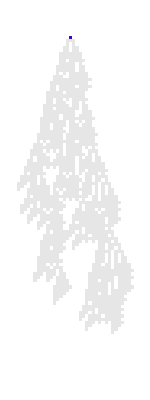
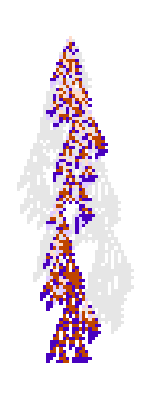
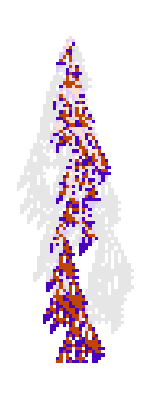
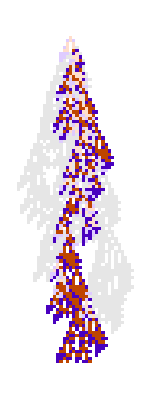
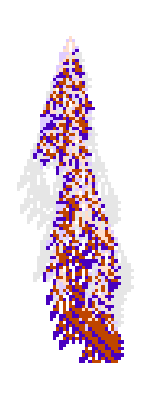
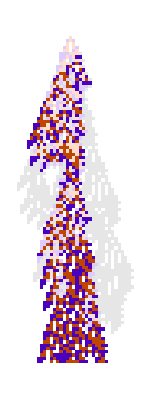
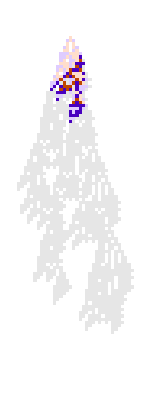
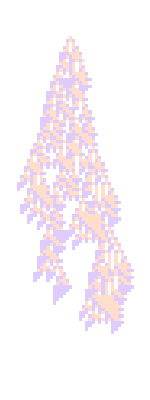

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 1, 1, 1]]
```

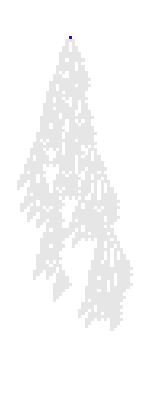
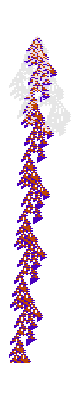
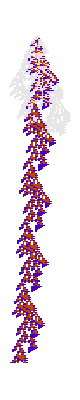
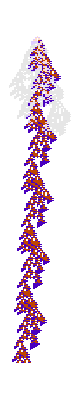
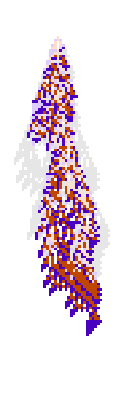
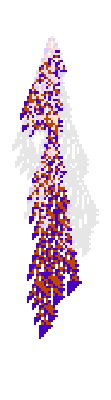
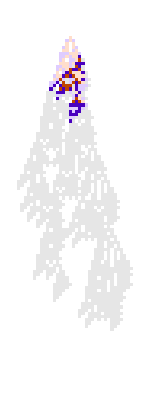
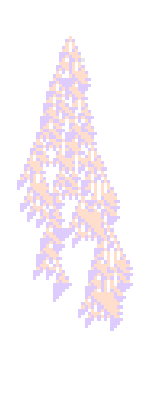
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 1, 1, 1]]
```

#### add1 Right 5

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 5, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Right 10

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 10, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 5, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 10

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 10, 1, 1]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

#### add1 Left 1

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 1, 1, 1]]
```

Integer[]

#### add1 Left 5

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 5, 1, 1]]
```

Integer[]

#### add1 Left 10

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 10, 1, 1]]
```

Integer[]

#### towhite Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  white[[All, 1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### towhite Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  white[[All, 5, 1, 1]]
```

#### tored Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  red[[All, 1, 1, 1]]
```

#### tored Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  red[[All, 5, 1, 1]]
```

### Increasing Disease Intensity

```mathematica
Length/@alldis[[1, All, 1, 1]]
```

{301,301,301,301,301,301,301,301,301,301}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[10, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[40, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[70, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Single Round

```mathematica
ResourceFunction["FoldGraph"][f,{x},{a,b,c},VertexLabels->Automatic]
```

-Graphics-

```mathematica
PerturbeRow[{initpat}]
```

PerturbeRow[test]

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
(*p = PerturbeRows[{{initpat, initpat}, ru, {1}}, 10->1];
p2 = PerturbeRows[{p[[1]], ru, {2}}, 10->1];*)
```

```mathematica
p = PerturbedCAEvolution[ru, {{1}, 0}, 100, {10->1, 15->1}];
```

$Aborted

```mathematica
pp1 = PerturbePoint[{initpat, ru}, {10, 1}, "PerturbationFunction"->]
```

add1

```mathematica
pp2 = PerturbePoint[pp1[[1]],{15,1}]
```

add1

```mathematica
pp = ResourceFunction["FoldGraph"][PerturbePoint[#1,#2, "PerturbationFunction"->flipall]&, {{initpat, ru}}, {{10, 1}, {15, 1}}]
```

flipall

flipall

flipall

-Graphics-

```mathematica
pp = ResourceFunction["FoldGraph"][PerturbeRow[#1,#2, "PerturbationFunction"->flipall]&, {{initpat, ru}}, {10->2, 15-> 2}]
```

-Graphics-

```mathematica
HighlightGraph[pp, VertexList[pp][[7]]]
```

-Graphics-

```mathematica
ShowCADiffs@@@Partition[VertexList[pp][[All, 1]], 2, 1]
```

{-Graphics-,-Graphics-}

```mathematica
Length[pp[[1]]]
```

2

```mathematica
ShowCADiffs[pp1[[1, 1]], pp2[[1, 1]]]
```

-Graphics-

```mathematica
Rest@ShowPerturbationEvolution[initpat, p]
```

{{{-Graphics-}},{{{-Graphics-}}}}

```mathematica
Replace[{10->1},x_Integer:>x->1,{1}]
```

{10→1}

```mathematica
Length[p[[2, 1, 1, 1]]]
```

101

```mathematica
Map[Length[#[[1]]]&, p]
```

{1,1}

```mathematica
Map[Length[#] &, p[[1, 1]], {1}]
```

{101}

```mathematica
getfirst[list_, level_]:= list[[#]]&@@Table[1, level]
```

```mathematica
getfirst[{{{1}}}, 1]
```

{{1}}

```mathematica
p[[#]]&@@Table[1, {1}[[1]]][[1]]
```

1

```mathematica
Map[ShowCADiffs[initpat,#] &, p[[2, 1]], {2}]
```

{{-Graphics-}}

```mathematica
ShowPerturbations[initpat, p[[2]], {2}]
```

{{-Graphics-}}

```mathematica
Map[ShowCADiffs[initpat, #]&, p2[[1]], {3}]
```

{{{-Graphics-}},{{-Graphics-}}}

```mathematica
Length[o[[1,2, 1]]]
```

101

```mathematica
Length[o[[1, 1]]]
```

1

```mathematica
p =PerturbeRow[pat,ru,10->1, "PerturbationStart"->"Center","PerturbationFunction"->flipall];
```

```mathematica
Options[ShowCADiffs]
```

{Trim→{1,10}}

2

```mathematica
plotca[pat]
```

-Graphics-

```mathematica
plotca@TrimCA[pat, {1, 10}]
```

-Graphics-

```mathematica
ShowCADiffs[pat, #]&@ p[[1]]
```

{}

{1,10}

-Graphics-

```mathematica
ArrayPlot[TrimCA[highlighted, {1, 10}], ColorRules->Join[#[[1]]*-1->#[[2]]&/@ customstyledata["Colors"], { -100->Black,_Integer->LightGray}]]
```

-Graphics-

#### All possible

```mathematica
ps = Table[PerturbePattern[{pat, ru},i->j, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->towhite], {i,5, 10}, {j,1, 10}];
```

```mathematica
ps = Table[PerturbePattern[{pat, ru}, {10, i}, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->add1], {i,1, 10}];
```

```mathematica
Map[showpatdiffs[pat, #, "Trim"->True]&,  ps[[ All, 1, 1]],{2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
t1_Integer : t1->1
```

## SW Notes

#### How to store results of perturbations

```mathematica
{1,2,0,1,p[0,1],XXXX}
```

```mathematica
p[_,1]->XXX
```

```mathematica
PerturbedCAEvolution[   ]
```

```mathematica
PerturbationIndicatorFunction->
```

```mathematica
p[0,1]
```

```mathematica
{0,1}
```

```mathematica
Apply[p]
```

```mathematica
Last
```

```mathematica
-#[[2]]&
```

```mathematica
<|0->XXX,1->2,2->0|>
```

#### How to specify perturbations

```mathematica
<|1->{{5,"Enumeration"}}|>
```

```mathematica
<|1->{{5,"Random"},{6,"Random"}}|>
```

```mathematica
<|1->{{5,f},{6,"Random"}}|>
```

```mathematica
5
```

```mathematica
{5,First}
```

```mathematica
Range[6]
```

{1,2,3,4,5,6}

```mathematica
Range[4,11]
```

{4,5,6,7,8,9,10,11}

```mathematica
First[ ]
```

```mathematica
Last[   ]
```

### Analysis functions

lifetime after perturbation   [ AKA fitness ]

number of cells that stay the same after perturbation

### ML for therapy

Fitness function is either (a) how many cells we can return to their original state, or (b) how close we can get the lifetime to the original